```mathematica
(*Load the packages*)
<<PhysicalConstants`;
<<Units`;
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
(*Define physical constants*)
alpha=FineStructureConstant;
c=SpeedOfLight//First;
eAu=ElectronCharge//First;
fPi=QuantityMagnitude[UnitConvert[Quantity[93, "MeV"], "eV"]];
gE=ElectronGFactor;
gP=ParticleData["Proton", "GFactor"];
h=PlanckConstant//First;
hbar=QuantityMagnitude[Quantity[1,"ReducedPlanckConstant"],"J*s"];
MSolar=QuantityMagnitude[Quantity[1, "SolarMass"], "Kilograms"];
mPl=PlanckMass//First;
mPi=QuantityMagnitude[UnitConvert[ParticleData["PiZero","Mass"], "eV/c^2"]];
muB=QuantityMagnitude[Quantity[1,"BohrMagneton"],"J/T"];
rE=BohrRadius//First;
```

```mathematica
(*Conversion factors*)
CToEv=(4*Pi*alpha)^(1/2)/eAu;
kgToEv=c^2/eAu;
mToEvMinus1=eAu/h/c;
JToEv=1/eAu;
pcToM=QuantityMagnitude[Quantity[1, "Parsecs"], "Meters"];
sToEvMinus1=eAu/(hbar);
TToEv2=kgToEv/CToEv/sToEvMinus1;
```

```mathematica
(*Define the vector field*)
Clear[BbarR,BbarTheta,BbarPhi,r,R,θ,ω];
F={BbarR,BbarTheta,BbarPhi}*(1+a*r^2)^(-4)*Exp[I*ω*Sqrt[R^2+r^2-2*r*R*Cos[θ]]];
curlF=FullSimplify[Curl[F,{r,θ,ϕ},"Spherical"]];
Print[curlF];
```

{(BbarPhi ⅇ^(ⅈ ω √(r^2+R^2-2 r R Cos[θ])) (√(r^2+R^2-2 r R Cos[θ]) Cot[θ]+ⅈ r R ω Sin[θ]))/(r (1+a r^2)^4 √(r^2+R^2-2 r R Cos[θ])),(BbarPhi ⅇ^(ⅈ ω √(r^2+R^2-2 r R Cos[θ])) (ⅈ r (1+a r^2) R ω Cos[θ]-√(r^2+R^2-2 r R Cos[θ])+r^2 (-ⅈ (1+a r^2) ω+7 a √(r^2+R^2-2 r R Cos[θ]))))/(r (1+a r^2)^5 √(r^2+R^2-2 r R Cos[θ])),(ⅇ^(ⅈ ω √(r^2+R^2-2 r R Cos[θ])) (ⅈ BbarTheta r^2 (1+a r^2) ω-ⅈ BbarTheta r (1+a r^2) R ω Cos[θ]+BbarTheta (1-7 a r^2) √(r^2+R^2-2 r R Cos[θ])-ⅈ BbarR r (1+a r^2) R ω Sin[θ]))/(r (1+a r^2)^5 √(r^2+R^2-2 r R Cos[θ]))}

```mathematica
(*Define the approximated integrand*)
integrand=(r*(ExpIntegralEi[I*ω*(R+r)]-ExpIntegralEi[I*ω*(R-r)])/(R*(1+a*r^2)^4))*2/Pi;
(*Perform the integration*)
integral=Integrate[integrand,r]
```

1/(48 a^2 π R)((8 a ⅇ^(-ⅈ (r-R) ω) (-1+a r R))/((1+a r^2) (1+a R^2)^2)+(8 a ⅇ^(ⅈ (r+R) ω) (1+a r R))/((1+a r^2) (1+a R^2)^2)+(2 a ⅇ^(ⅈ (r+R) ω) (2+2 a r R+(1+a r^2) (3 a r R-ⅈ (r-R) ω)))/((1+a r^2)^2 (1+a R^2))-(2 a ⅇ^(-ⅈ (r-R) ω) (2-2 a r R-(1+a r^2) (3 a r R-ⅈ (r+R) ω)))/((1+a r^2)^2 (1+a R^2))-(16 a ExpIntegralEi[-ⅈ (r-R) ω])/((1+a R^2)^3)+(16 a ExpIntegralEi[ⅈ (-r+R) ω])/((1+a r^2)^3)-(16 a ExpIntegralEi[ⅈ (r+R) ω])/((1+a r^2)^3)+(16 a ExpIntegralEi[ⅈ (r+R) ω])/((1+a R^2)^3)+(8 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (ExpIntegralEi[(1/(√a)-ⅈ r) ω]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)-ⅈ r ω]))/((1+a R^2)^3)+(4 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (ExpIntegralEi[(1/(√a)-ⅈ r) ω]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)-ⅈ r ω]))/((1+a R^2)^2)+(3 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (ExpIntegralEi[(1/(√a)-ⅈ r) ω]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)-ⅈ r ω]))/(1+a R^2)+(4 √a ⅇ^(-ω/(√a)+ⅈ R ω) ω (ExpIntegralEi[(1/(√a)-ⅈ r) ω]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)-ⅈ r ω]))/((1+a R^2)^2)+(√a ⅇ^(-ω/(√a)+ⅈ R ω) ω (ExpIntegralEi[(1/(√a)-ⅈ r) ω]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)-ⅈ r ω]))/(1+a R^2)+(ⅈ √a ⅇ^(-ω/(√a)+ⅈ R ω) R ω^2 (ExpIntegralEi[(1/(√a)-ⅈ r) ω]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)-ⅈ r ω]))/(1+a R^2)+(8 a ⅇ^(-ω/(√a)+ⅈ R ω) (ExpIntegralEi[(1/(√a)-ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)-ⅈ r ω]))/((1+a R^2)^3)+(4 ⅈ a ⅇ^(-ω/(√a)+ⅈ R ω) R ω (ExpIntegralEi[(1/(√a)-ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)-ⅈ r ω]))/((1+a R^2)^2)+(3 ⅈ a ⅇ^(-ω/(√a)+ⅈ R ω) R ω (ExpIntegralEi[(1/(√a)-ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)-ⅈ r ω]))/(1+a R^2)+(ⅇ^(-ω/(√a)+ⅈ R ω) ω^2 (ExpIntegralEi[(1/(√a)-ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)-ⅈ r ω]))/(1+a R^2)+(8 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (-ExpIntegralEi[(1/(√a)+ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ⅈ r ω]))/((1+a R^2)^3)+(4 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (-ExpIntegralEi[(1/(√a)+ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ⅈ r ω]))/((1+a R^2)^2)+(3 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (-ExpIntegralEi[(1/(√a)+ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ⅈ r ω]))/(1+a R^2)+(4 √a ⅇ^(-ω/(√a)+ⅈ R ω) ω (-ExpIntegralEi[(1/(√a)+ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ⅈ r ω]))/((1+a R^2)^2)+(√a ⅇ^(-ω/(√a)+ⅈ R ω) ω (-ExpIntegralEi[(1/(√a)+ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ⅈ r ω]))/(1+a R^2)+(ⅈ √a ⅇ^(-ω/(√a)+ⅈ R ω) R ω^2 (-ExpIntegralEi[(1/(√a)+ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ⅈ r ω]))/(1+a R^2)-(8 a ⅇ^(-ω/(√a)+ⅈ R ω) (ExpIntegralEi[(1/(√a)+ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ⅈ r ω]))/((1+a R^2)^3)-(4 ⅈ a ⅇ^(-ω/(√a)+ⅈ R ω) R ω (ExpIntegralEi[(1/(√a)+ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ⅈ r ω]))/((1+a R^2)^2)-(3 ⅈ a ⅇ^(-ω/(√a)+ⅈ R ω) R ω (ExpIntegralEi[(1/(√a)+ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ⅈ r ω]))/(1+a R^2)-(ⅇ^(-ω/(√a)+ⅈ R ω) ω^2 (ExpIntegralEi[(1/(√a)+ⅈ r) ω]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ⅈ r ω]))/(1+a R^2))

```mathematica
(*Substitute r=0 into the integral*)
integral0=integral /. r->0;
integral0=Simplify[integral0]
```

0

```mathematica
(*Common parameters*)
Bbar=10^-10;(*Background magnetic field (T)*)
BbarR=Bbar;
magX=2.03*10^26;(*Calculate distance of L1544 from Galactic Centre (eV^-1)*)

(*Parameters of flat potential*)
f=1*10^26; (*Energy scale of axion (eV)*)
mA=1*10^-22; (*Axion mass, 1e-18 to 1e-22 (eV)*)
mD=1*10^-22; (*Dark photon mass, 1e-18 to 1e-22 (eV)*)
mU=1*10^-6*mD; (*Chemical potential of dark photon (eV)*)
rcPc=180; (*Core radius (pc)*)

(*Calculate mass density of axion field (eV^4)*)
rho0=1.9*(mA/10^-23)^(-2)*(rcPc/10^3)^(-4)*MSolar;
rho0*=kgToEv*(pcToM*mToEvMinus1)^(-3);

(*Scaling constants*)
aA=(9.1*10^-2/rcPc^2)*(pcToM*mToEvMinus1)^(-2); (*Scaling constant of axion (eV^2)*)
aD=aA; (*Scaling constant of dark photon (eV^2)*)

(*Core radius (eV^-1)*)
rc=rcPc*pcToM*mToEvMinus1;

(*Calculate amplitudes*)
phi0=Sqrt[2*rho0]/mA; (*Amplitude of axion potential (eV)*)
XBar=phi0; (*Amplitude of dark photon potential (eV)*)

(*Coupling constants and frequencies*)
gAc=alpha/Pi/f; (*Coupling constant (eV^-1)*)
epsilon=1*10^-3; (*Coupling strength, 1e-3 to 1e-5*)
omegaA=mA; (*Oscillation frequency of axion (eV)*)
omegaD=mD-mU; (*Oscillation frequency of dark photon (eV)*)
```

```mathematica
(*Substitute the upper boundary of the integral*)
integralInf=integral/.r->10^12*rc;

(*Evaluate the integral numerically by substituting the values of a,R,and ω*)
IPhi3=integralInf/.{a->aA, R->magX, ω->omegaA};

(*Print the results*)
Print[IPhi3];
Print[Abs[IPhi3]]
```

General::munfl: Exp[-1485.03+20300. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1518.77-4.47978×10^14 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1485.03+20300. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-4.23848×10^11+1.09237×10^17 ⅈ

1.09237×10^17

```mathematica
(*Calculate the magnitude of the magnetic field in the phi direction*)
BPhi3=omegaA*gAc*phi0*1/2*(-I BbarR*magX*omegaA)*IPhi3;
(*Calculate the absolute value of the magnetic field*)
Abs[BPhi3]
```

4.16811×10^-18

```mathematica
(*Substitute the upper boundary of the integral with infinity*)
integralInf=integral/.r->Infinity
```

1/(48 a^2 π R)((8 a ⅇ^(ω ((-ⅈ) ∞)) (-1+a R ∞))/((1+a R^2)^2 (1+a ∞))+(8 a ⅇ^(ω (ⅈ ∞)) (1+a R ∞))/((1+a R^2)^2 (1+a ∞))-(2 a ⅇ^(ω ((-ⅈ) ∞)) (2+a R (-∞)-(1+a ∞) (ω ((-ⅈ) ∞)+a R ∞)))/((1+a R^2) (1+a ∞)^2)+(2 a ⅇ^(ω (ⅈ ∞)) (2+a R ∞+(1+a ∞) (ω ((-ⅈ) ∞)+a R ∞)))/((1+a R^2) (1+a ∞)^2)-(16 a ExpIntegralEi[ω ((-ⅈ) ∞)])/((1+a R^2)^3)+(16 a ExpIntegralEi[ω ((-ⅈ) ∞)])/(1+a ∞)^3+(8 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (ExpIntegralEi[ω ((-ⅈ) ∞)]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω ((-ⅈ) ∞)]))/((1+a R^2)^3)+(4 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (ExpIntegralEi[ω ((-ⅈ) ∞)]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω ((-ⅈ) ∞)]))/((1+a R^2)^2)+(3 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (ExpIntegralEi[ω ((-ⅈ) ∞)]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω ((-ⅈ) ∞)]))/(1+a R^2)+(4 √a ⅇ^(-ω/(√a)+ⅈ R ω) ω (ExpIntegralEi[ω ((-ⅈ) ∞)]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω ((-ⅈ) ∞)]))/((1+a R^2)^2)+(√a ⅇ^(-ω/(√a)+ⅈ R ω) ω (ExpIntegralEi[ω ((-ⅈ) ∞)]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω ((-ⅈ) ∞)]))/(1+a R^2)+(ⅈ √a ⅇ^(-ω/(√a)+ⅈ R ω) R ω^2 (ExpIntegralEi[ω ((-ⅈ) ∞)]-ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω ((-ⅈ) ∞)]))/(1+a R^2)+(8 a ⅇ^(-ω/(√a)+ⅈ R ω) (ExpIntegralEi[ω ((-ⅈ) ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω ((-ⅈ) ∞)]))/((1+a R^2)^3)+(4 ⅈ a ⅇ^(-ω/(√a)+ⅈ R ω) R ω (ExpIntegralEi[ω ((-ⅈ) ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω ((-ⅈ) ∞)]))/((1+a R^2)^2)+(3 ⅈ a ⅇ^(-ω/(√a)+ⅈ R ω) R ω (ExpIntegralEi[ω ((-ⅈ) ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω ((-ⅈ) ∞)]))/(1+a R^2)+(ⅇ^(-ω/(√a)+ⅈ R ω) ω^2 (ExpIntegralEi[ω ((-ⅈ) ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω ((-ⅈ) ∞)]))/(1+a R^2)+(16 a ExpIntegralEi[ω (ⅈ ∞)])/((1+a R^2)^3)-(16 a ExpIntegralEi[ω (ⅈ ∞)])/(1+a ∞)^3+(8 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (-ExpIntegralEi[ω (ⅈ ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω (ⅈ ∞)]))/((1+a R^2)^3)+(4 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (-ExpIntegralEi[ω (ⅈ ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω (ⅈ ∞)]))/((1+a R^2)^2)+(3 ⅈ a^(3/2) ⅇ^(-ω/(√a)+ⅈ R ω) R (-ExpIntegralEi[ω (ⅈ ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω (ⅈ ∞)]))/(1+a R^2)+(4 √a ⅇ^(-ω/(√a)+ⅈ R ω) ω (-ExpIntegralEi[ω (ⅈ ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω (ⅈ ∞)]))/((1+a R^2)^2)+(√a ⅇ^(-ω/(√a)+ⅈ R ω) ω (-ExpIntegralEi[ω (ⅈ ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω (ⅈ ∞)]))/(1+a R^2)+(ⅈ √a ⅇ^(-ω/(√a)+ⅈ R ω) R ω^2 (-ExpIntegralEi[ω (ⅈ ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω (ⅈ ∞)]))/(1+a R^2)-(8 a ⅇ^(-ω/(√a)+ⅈ R ω) (ExpIntegralEi[ω (ⅈ ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω (ⅈ ∞)]))/((1+a R^2)^3)-(4 ⅈ a ⅇ^(-ω/(√a)+ⅈ R ω) R ω (ExpIntegralEi[ω (ⅈ ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω (ⅈ ∞)]))/((1+a R^2)^2)-(3 ⅈ a ⅇ^(-ω/(√a)+ⅈ R ω) R ω (ExpIntegralEi[ω (ⅈ ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω (ⅈ ∞)]))/(1+a R^2)-(ⅇ^(-ω/(√a)+ⅈ R ω) ω^2 (ExpIntegralEi[ω (ⅈ ∞)]+ⅇ^((2 ω)/(√a)) ExpIntegralEi[-ω/(√a)+ω (ⅈ ∞)]))/(1+a R^2))

```mathematica
(*Define the integral when r tends to infinity*)
integralInf=Hold[1/(24Pi a^2*R)*((
16a/(1+a*R^2)^3*(Pi I))+
8I a^(3/2)Exp[-ω/Sqrt[a]+I R*ω]R(Exp[2ω/Sqrt[a]]-1)/(1+a*R^2)^3*(Pi I)+
4I a^(3/2)Exp[-ω/Sqrt[a]+I R*ω]R(Exp[2ω/Sqrt[a]]-1)/(1+a*R^2)^2*(Pi I)+
3I a^(3/2)Exp[-ω/Sqrt[a]+I R*ω]R(Exp[2ω/Sqrt[a]]-1)/(1+a*R^2)*(Pi I)+
4 a^(1/2)Exp[-ω/Sqrt[a]+I R*ω]ω(Exp[2ω/Sqrt[a]]-1)/(1+a*R^2)^2*(Pi I)+
a^(1/2)Exp[-ω/Sqrt[a]+I R*ω]ω(Exp[2ω/Sqrt[a]]-1)/(1+a*R^2)*(Pi I)+
I a^(1/2)Exp[-ω/Sqrt[a]+I R*ω]R*ω^2(Exp[2ω/Sqrt[a]]-1)/(1+a*R^2)*(Pi I)-
8a Exp[-ω/Sqrt[a]+I R*ω](Exp[2ω/Sqrt[a]]+1)/(1+a*R^2)^3*(Pi I)-
4I a Exp[-ω/Sqrt[a]+I R*ω]R*ω(Exp[2ω/Sqrt[a]]+1)/(1+a*R^2)^2*(Pi I)-
3I a Exp[-ω/Sqrt[a]+I R*ω]R*ω(Exp[2ω/Sqrt[a]]+1)/(1+a*R^2)*(Pi I)-
Exp[-ω/Sqrt[a]+I R*ω]ω^2(Exp[2ω/Sqrt[a]]+1)/(1+a*R^2)*(Pi I))];
(*Evaluate the integral numerically by substituting the values of a, R, and ω*)
IPhi3=ReleaseHold[integralInf]/.{a->aA, R->magX, ω->omegaA}
```

General::munfl: Exp[-1485.03+20300. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.+1.09237×10^17 ⅈ

```mathematica
(*Calculate the magnitude of the magnetic field in the phi direction*)
BPhi3=omegaA*gAc*phi0*1/2*(-I BbarR*magX*omegaA)*IPhi3;
(*Calculate the absolute value of the magnetic field*)
Abs[BPhi3]
```

4.16812×10^-18

```mathematica
(*Simplify the integral*)
integralInf=FullSimplify[ReleaseHold[integralInf]]
```

1/(24 a^2 R (1+a R^2)^3)ⅇ^(-ω/(√a)) (16 ⅈ a ⅇ^(ω/(√a))-3 a^(7/2) ⅇ^(ⅈ R ω) (-1+ⅇ^((2 ω)/(√a))) R^5+3 a^3 ⅇ^(ⅈ R ω) (1+ⅇ^((2 ω)/(√a))) R^5 ω-ⅈ ⅇ^(ⅈ R ω) (1+ⅇ^((2 ω)/(√a))) ω^2+a^2 ⅇ^(ⅈ R ω) (1+ⅇ^((2 ω)/(√a))) R^3 ω (10-ⅈ R ω)-√a ⅇ^(ⅈ R ω) (-1+ⅇ^((2 ω)/(√a))) ω (-5 ⅈ+R ω)+a ⅇ^(ⅈ R ω) (1+ⅇ^((2 ω)/(√a))) (-8 ⅈ+R ω (7-2 ⅈ R ω))-a^(5/2) ⅇ^(ⅈ R ω) (-1+ⅇ^((2 ω)/(√a))) R^3 (10+R ω (-ⅈ+R ω))-a^(3/2) ⅇ^(ⅈ R ω) (-1+ⅇ^((2 ω)/(√a))) R (15+2 R ω (-3 ⅈ+R ω)))

```mathematica
(*Convert the simplified integral to LaTeX code*)
TeXForm[integralInf]
```

\frac{e^{-\frac{\omega }{\sqrt{a}}} \left(-3 a^{7/2} R^5 \left(e^{\frac{2 \omega }{\sqrt{a}}}-1\right) e^{i R \omega }-a^{5/2} R^3 \left(e^{\frac{2 \omega
   }{\sqrt{a}}}-1\right) e^{i R \omega } (10+R \omega  (R \omega -i))-a^{3/2} R \left(e^{\frac{2 \omega }{\sqrt{a}}}-1\right) e^{i R \omega } (15+2 R \omega  (R \omega
   -3 i))+3 a^3 R^5 \omega  \left(e^{\frac{2 \omega }{\sqrt{a}}}+1\right) e^{i R \omega }+a^2 R^3 \omega  \left(e^{\frac{2 \omega }{\sqrt{a}}}+1\right) e^{i R \omega }
   (10-i R \omega )-i \omega ^2 \left(e^{\frac{2 \omega }{\sqrt{a}}}+1\right) e^{i R \omega }-\sqrt{a} \omega  \left(e^{\frac{2 \omega }{\sqrt{a}}}-1\right) e^{i R
   \omega } (R \omega -5 i)+a \left(e^{\frac{2 \omega }{\sqrt{a}}}+1\right) e^{i R \omega } (R \omega  (7-2 i R \omega )-8 i)+16 i a e^{\frac{\omega
   }{\sqrt{a}}}\right)}{24 a^2 R \left(a R^2+1\right)^3}

```mathematica
(*Define the exact integrand*)
integrand=Exp[I*ω*Sqrt[R^2+r^2-2*r*R*Cos[θ]]]*Sin[θ]^2*r^2/((1+a*r^2)^4*(R^2+r^2-2*r*R*Cos[θ]));
(*Substitute values*)
integrand=integrand/. {ω->omegaA,R->magX,a->aA};
Print[integrand]
```

(ⅇ^((ⅈ √(4.1209×10^52+r^2-4.06×10^26 r Cos[θ]))/10000000000000000000000) r^2 Sin[θ]^2)/((1+4.53448×10^-51 r^2)^4 (4.1209×10^52+r^2-4.06×10^26 r Cos[θ]))

```mathematica
(*Inner integral over θ*)
innerIntegral[r_]:=NIntegrate[integrand/. r->r,{θ,0,π},Method->"DoubleExponentialOscillatory", WorkingPrecision->20, PrecisionGoal->10, MaxRecursion->20];
(*Outer integral over r*)
integral=NIntegrate[innerIntegral[r],{r,0,10^12*rc},Method->"GaussKronrodRule", WorkingPrecision->20, PrecisionGoal->10, MaxRecursion->20];
(*Print the results*)
Print[integral];
Print[Abs[integral]];
```

NIntegrate::precw: The precision of the argument function ((ⅇ^((ⅈ √(4.1209×10^52+r^2-4.06×10^26 r Cos[θ]))/10000000000000000000000) r^2 Sin[θ]^2)/((1+4.53448×10^-51 r^2)^4 (4.1209×10^52+r^2-4.06×10^26 r Cos[θ]))) is less than WorkingPrecision (20.).

NIntegrate::oscir: Method DoubleExponentialOscillatory works only for one-dimensional integrals with infinite ranges.

NIntegrate::inumr: The integrand (2.7182818284590452354^((ⅈ √(«1»))/10000000000000000000000) r^2 Sin[θ]^2)/((1+4.5344841962936210371×10^-51 r^2)^4 (4.1209000000000003474×10^52+r^2-4.0600000000000001144×10^26 r Cos[θ])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.1415926535897932385}}.

NIntegrate::precw: The precision of the argument function ((ⅇ^((ⅈ √(4.1209×10^52+r^2-4.06×10^26 r Cos[θ]))/10000000000000000000000) r^2 Sin[θ]^2)/((1+4.53448×10^-51 r^2)^4 (4.1209×10^52+r^2-4.06×10^26 r Cos[θ]))) is less than WorkingPrecision (20.).

NIntegrate::oscir: Method DoubleExponentialOscillatory works only for one-dimensional integrals with infinite ranges.

NIntegrate::inumr: The integrand (2.7182818284590452354^((ⅈ √(«1»))/10000000000000000000000) r^2 Sin[θ]^2)/((1+4.5344841962936210371×10^-51 r^2)^4 (4.1209000000000003474×10^52+r^2-4.0600000000000001144×10^26 r Cos[θ])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.1415926535897932385}}.

NIntegrate::precw: The precision of the argument function ((ⅇ^((ⅈ √(4.1209×10^52+r^2-4.06×10^26 r Cos[θ]))/10000000000000000000000) r^2 Sin[θ]^2)/((1+4.53448×10^-51 r^2)^4 (4.1209×10^52+r^2-4.06×10^26 r Cos[θ]))) is less than WorkingPrecision (20.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::oscir: Method DoubleExponentialOscillatory works only for one-dimensional integrals with infinite ranges.

General::stop: Further output of NIntegrate::oscir will be suppressed during this calculation.

NIntegrate::inumr: The integrand (2.7182818284590452354^((ⅈ √(«1»))/10000000000000000000000) r^2 Sin[θ]^2)/((1+4.5344841962936210371×10^-51 r^2)^4 (4.1209000000000003474×10^52+r^2-4.0600000000000001144×10^26 r Cos[θ])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.1415926535897932385}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

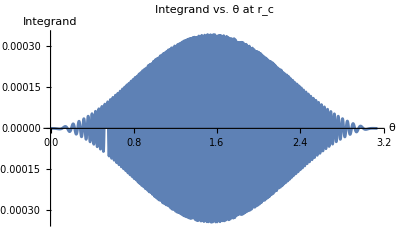

-Graphics3D-

```mathematica
(*Plotting the integrand*)
Plot[Evaluate[Re[integrand/.r->rc]],{θ,0,π},PlotRange->All,AxesLabel->{"θ","Integrand"},PlotLabel->Row[{"Integrand vs. θ at ",Subscript[r,HoldForm[c]]}],Filling->Axis](*Generate values for the integrand over the surface*)
Plot3D[Abs[integrand],{r,0,10^12*rc},{θ,0,Pi},PlotRange->All,AxesLabel->{"r","θ","Integrand"},Mesh->None,PlotStyle->Opacity[0.8],AspectRatio->Automatic]
```